```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return[solution]
];
```

```mathematica
Plots[data_List]:= ListPlot[#⟦2⟧ &/@ data, PlotRange->All, ImageSize->500, GridLines->Automatic, Ticks->{Table[i, {i, 0, 200, 20}], {0, 1}}]
```

## Точные решения

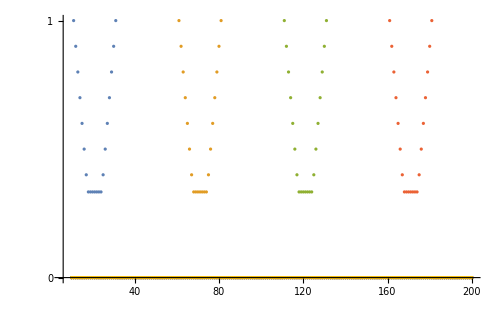

```mathematica
advection = NormalRepresentation@Import["advection.json"] ;
Plots[advection]
```

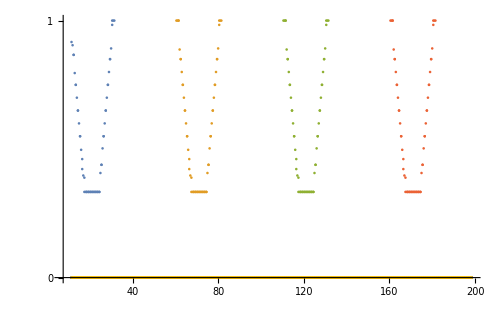

```mathematica
advectionPPM = NormalRepresentation@Import["advectionPPM.json"] ;
ppmPlot =Plots[advectionPPM]
```

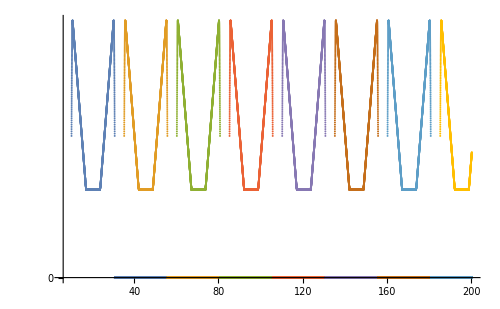

```mathematica
advectionPPML = NormalRepresentation@Import["advectionPPML.json"] ;
ppmlPlot = Plots[advectionPPML]
```

```mathematica
If[True ,
FileExport[ppmPlot, "advection_ppm.pdf", "PDF"];
FileExport[ppmlPlot, "advection_ppml.pdf", "PDF"];
];
```

```mathematica
Sort@advection⟦1,2, 1;;23⟧
```

{{10.,0.},{11.,1.},{12.,0.9},{13.,0.8},{14.,0.7},{15.,0.6},{16.,0.5},{17.,0.4},{18.,0.333333},{19.,0.333333},{20.,0.333333},{21.,0.333333},{22.,0.333333},{23.,0.333333},{24.,0.333333},{25.,0.4},{26.,0.5},{27.,0.6},{28.,0.7},{29.,0.8},{30.,0.9},{31.,1.},{32.,0.}}

```mathematica
Sort@advectionPPML⟦1,2, 1;;70⟧
```

{{10.26,0.554825},{10.27,0.5718},{10.28,0.588425},{10.29,0.6047},{10.3,0.620625},{10.31,0.6362},{10.32,0.651425},{10.33,0.6663},{10.34,0.680825},{10.35,0.695},{10.36,0.708825},{10.37,0.7223},{10.38,0.735425},{10.39,0.7482},{10.4,0.760625},{10.41,0.7727},{10.42,0.784425},{10.43,0.7958},{10.44,0.806825},{10.45,0.8175},{10.46,0.827825},{10.47,0.8378},{10.48,0.847425},{10.49,0.8567},{10.5,0.865625},{10.51,0.8742},{10.52,0.882425},{10.53,0.8903},{10.54,0.897825},{10.55,0.905},{10.56,0.911825},{10.57,0.9183},{10.58,0.924425},{10.59,0.9302},{10.6,0.935625},{10.61,0.9407},{10.62,0.945425},{10.63,0.9498},{10.64,0.953825},{10.65,0.9575},{10.66,0.960825},{10.67,0.9638},{10.68,0.966425},{10.69,0.9687},{10.7,0.970625},{10.71,0.9722},{10.72,0.973425},{10.73,0.9743},{10.74,0.974825},{10.76,0.974},{10.77,0.973},{10.78,0.972},{10.79,0.971},{10.8,0.97},{10.81,0.969},{10.82,0.968},{10.83,0.967},{10.84,0.966},{10.85,0.965},{10.86,0.964},{10.87,0.963},{10.88,0.962},{10.89,0.961},{10.9,0.96},{10.91,0.959},{10.92,0.958},{10.93,0.957},{10.94,0.956},{10.95,0.955},{10.96,0.954}}

```mathematica
Sort@advectionPPM⟦2,2, 148;;218⟧
```

{{60.5,1.},{61.,1.},{61.5,1.},{61.5,1.},{62.,0.8875},{62.5,0.85},{62.5,0.85},{63.,0.8},{63.5,0.75},{63.5,0.75},{64.,0.7},{64.5,0.65},{64.5,0.65},{65.,0.6},{65.5,0.55},{65.5,0.55},{66.,0.497222},{66.5,0.461111},{66.5,0.422222},{67.,0.397222},{67.5,0.388889},{67.5,0.333333},{68.,0.333333},{68.5,0.333333},{68.5,0.333333},{69.,0.333333},{69.5,0.333333},{69.5,0.333333},{70.,0.333333},{70.5,0.333333},{70.5,0.333333},{71.,0.333333},{71.5,0.333333},{71.5,0.333333},{72.,0.333333},{72.5,0.333333},{72.5,0.333333},{73.,0.333333},{73.5,0.333333},{73.5,0.333333},{74.,0.333333},{74.5,0.333333},{74.5,0.333333},{75.,0.406944},{75.5,0.438889},{75.5,0.438889},{76.,0.502778},{76.5,0.55},{76.5,0.55},{77.,0.6},{77.5,0.65},{77.5,0.65},{78.,0.7},{78.5,0.75},{78.5,0.75},{79.,0.8},{79.5,0.85},{79.5,0.85},{80.,0.891667},{80.5,0.983333},{80.5,1.},{81.,1.},{81.5,1.},{81.5,0.},{82.,0.},{82.5,0.},{82.5,0.},{83.,0.},{83.5,0.},{83.5,0.},{84.,0.}}